## Projection of a circle onto a line

```mathematica
equation of a circle
```

```mathematica
P=R Cos[t]u + R sin[t]n×u+C
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{t,0,2π}]
```

```mathematica
projection of circle onto a line
```

To uniquely identify the angle of a marker, we need
 1.) to know the center of its circle  C_xyz, 
 2.) at least two non-parallel, nonsingular (not parallel with normal to circle n_c), scans that do not overlap other marker paths. p_1 p_2
 
 Parallel if cross product is zero.
|uxv|	=	|u||v|sintheta

```mathematica
|u×v| = |u|  |v| Sin[θ]
```

```mathematica
A.B = ||A|| ||B|| Cos[θ]  (zero if perpendicular)
```

```mathematica
The size of the projection is 2r Sin[θ], where θ is the angle between n and Subscript[p, i].  The center of the projection is at  Subscript[C, xyz].n
```

```mathematica
{a,b,c}.{d,e,f}
```

a d+b e+c f

```mathematica
Manipulate[Module[{C3,n,u,v,lat,long},
C3 = {Cxy⟦1⟧,Cxy⟦2⟧,Cz};
long = n12⟦1⟧;
lat =n12⟦2⟧;
n = {Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u ={-Sin[long],Cos[long],0};
v = {Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
Show[{ParametricPlot3D[C3+Cos[θ]u+Sin[θ] v,
{θ,0,2π},PlotStyle->Thick,PlotRange-> {{-2,2},{-2,2},{-2,2}}
],
Graphics3D[{
Blue,Arrow[{{0,0,0},C3}],
Red,Arrow[{C3,C3+n}],
Purple,Arrow[{C3,C3+u}],
Green,Arrow[{C3,C3+v}]
}]
}]],
Row[{}],
{{Cxy,{0,0},"C_xy"},{-1,-1},{1,1},ControlType->Slider2D},
{{n12,{0,0},"n"},{-π,π},{π,0},ControlType->Slider2D},
{{Cz,0,"C_z"},-1,1,ControlType->VerticalSlider,ControlPlacement->Left}]
```

```mathematica
Manipulate[Module[{tr,C3,n,u,v,lat,long},
tr = 1/12; (*radius of torus*)
C3 = {Cxy⟦1⟧,Cxy⟦2⟧,Cz};
lat = n12⟦1⟧;
long =n12⟦2⟧;
n = {Cos[lat] Sin[long],Sin[lat] Sin[long],Cos[long]}; (*normal to circle*)
u ={-Sin[lat],Cos[lat],0};
v = {Cos[lat] Cos[long],Cos[long] Sin[lat],-Sin[long]}; (*v =  n×u *)
Show[{ParametricPlot3D[C3+(1+tr Cos[v])Cos[θ]u+(1+tr Cos[v])Sin[θ] n×u +tr Sin[v]n,
{θ,0,2π},{v,0,2Pi},Mesh-> None,PlotRange-> {{-2-tr,2+tr},{-2-tr,2+tr},{-2-tr,2+tr}}
],
Graphics3D[{Arrowheads[0.05],
Blue,Arrow[Tube[{{0,0,0},C3},0.04]],
Red,Arrow[Tube[{C3,C3+n},0.04]],
Purple,Arrow[Tube[{C3,C3+u},0.03]],
Green,Arrow[Tube[{C3,C3+v},0.03]]
}]
}]],
(*TODO: project onto a line *)
{{Cxy,{0,0},"C_xy"},{-1,-1},{1,1},ControlType->Slider2D},
{{n12,{0,0},"n"},{-π,π},{π,0},ControlType->Slider2D},
{{Cz,0,"C_z"},-1,1,ControlType->VerticalSlider,ControlPlacement->Left}]
```

```mathematica
RotationMatrix[lat,{0,0,1}].RotationMatrix[long,{0,1,0}]//MatrixForm
```

(Cos[lat] Cos[long] | -Sin[lat] | Cos[lat] Sin[long]
Cos[long] Sin[lat] | Cos[lat] | Sin[lat] Sin[long]
-Sin[long] | 0 | Cos[long])

```mathematica
Manipulate[Module[{tr,C3,n,u,v,lat,long,projV},
tr = 1/16; (*radius of torus*)
C3 = {Cxy⟦1⟧,Cxy⟦2⟧,Cz};
long = n12⟦1⟧;
lat =n12⟦2⟧;
n = {Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u ={-Sin[long],Cos[long],0};
v = {Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
projV = {Cos[ proj⟦1⟧] Sin[proj⟦2⟧],Sin[proj⟦1⟧] Sin[proj⟦2⟧],Cos[proj⟦2⟧]};
(*Column[{*)
Show[{ParametricPlot3D[C3+(1+tr Cos[v])Cos[θ]u+(1+tr Cos[v])Sin[θ] n×u +tr Sin[v]n,
{θ,0,2π},{v,0,2Pi},Mesh-> None,PlotRange-> {{-2-tr,2+tr},{-2-tr,2+tr},{-2-tr,2+tr}},
AxesLabel->{"x","y","z"}
],
Graphics3D[{Arrowheads[0.05],
Blue,Arrow[Tube[{{0,0,0},C3},0.04]],
Red,Arrow[Tube[{C3,C3+n},0.04]],
Purple,Arrow[Tube[{C3,C3+u},0.03]],
Green,Arrow[Tube[{C3,C3+v},0.03]],
(*Black,Arrow[Tube[{{0,0,0},2projV},0.04]]*)
}]
}]

(*,Plot[(C3+Cos[θ]u+Sin[θ] v).projV,{θ,0,2π}]
}]*)
],
(*TODO: project onto a line *)
Row[{Panel[Control[{{Cxy,{0,0},{"C_xy","a"}},{-1,-1},{1,1},ControlType->Slider2D}]],Spacer[20],
Control[{{Cz,0,"C_z"},-1,1,ControlType->VerticalSlider,ImageSize-> Tiny}],Spacer[20],
Control[{{n12,{0,0},"n"},{-π,π},{π,0},ControlType->Slider2D}],Spacer[20](*,
Control[{{proj,{0,0},"proj"},{-π,π},{π,0},ControlType->Slider2D}]*)
}],
{{Cxy,{0,0},{"C_xy","a"}},{-1,-1},{1,1},ControlType->None},
{{n12,{0,0},"normal vector"},{-π,π},{π,0},ControlType->None},
{{proj,{0,0},"proj"},{-π,π},{π,0},ControlType->None},
{{Cz,0,"C_z"},-1,1,ControlType->None}]
```

```mathematica
n = {Cos[lat] Sin[long],Sin[lat] Sin[long],Cos[long]}; (*normal to circle*)
u ={-Sin[lat],Cos[lat],0};
v = {Cos[lat] Cos[long],Cos[long] Sin[lat],-Sin[long]}; (*v =  n×u *)
FullSimplify[(C3+Cos[θ]u+Sin[θ] v).{p1,p2,p3}]
```

p1 (0.75-1. Cos[θ] Sin[lat]+Cos[lat] Cos[long] Sin[θ])+p2 (0.95+Cos[lat] Cos[θ]+Cos[long] Sin[lat] Sin[θ])+p3 (0.89-1. Sin[long] Sin[θ])

```mathematica
Minimize[{({c1,c2,c3}+Cos[θ]u+Sin[θ] v).{p1,p2,p3},θ>-π ,θ<π},{θ},Reals]
```

Minimize[{p1 (c1-Cos[θ] Sin[lat]+Cos[lat] Cos[long] Sin[θ])+p2 (c2+Cos[lat] Cos[θ]+Cos[long] Sin[lat] Sin[θ])+p3 (c3-Sin[long] Sin[θ]),θ>-π,θ<π},{θ},Reals]

```mathematica
({c1,c2,c3}+Cos[θ]u+Sin[θ] v)//MatrixForm
```

(c1-Cos[θ] Sin[lat]+Cos[lat] Cos[long] Sin[θ]
c2+Cos[lat] Cos[θ]+Cos[long] Sin[lat] Sin[θ]
c3-Sin[long] Sin[θ])

```mathematica
√2
```

√2

### Project Circles onto Plane for Needle Steering

```mathematica
CircleEq[C3_,lat_,long_,rad_,θ_]:=Module[{n,u,v},
n = {Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u ={-Sin[long],Cos[long],0};
v = {Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
C3+rad Cos[θ]u+rad Sin[θ] v];
CircleEq3[C3_,lat_,long_,rad_,θ_,θx_,θy_]:=Module[{n,u,v,RotM,C3rot,xyzNorm,x,y,z},
x=Cos[θx] Sin[θy];
y=-Cos[θy] Sin[θx];
z=Cos[θx] Cos[θy];
xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2);
RotM = RotationMatrix[ArcTan[z,x],{0,1,0}].RotationMatrix[ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}];
n =RotM.{Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u =RotM.{-Sin[long],Cos[long],0};
v = RotM.{Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
C3rot = RotM.C3;
C3rot+rad Cos[θ]u+rad Sin[θ] v];
CenterCircleEq3[C3_,lat_,long_,rad_,θ_,θx_,θy_]:=Module[{RotM,xyzNorm,x,y,z},
x=Cos[θx] Sin[θy];
y=-Cos[θy] Sin[θx];
z=Cos[θx] Cos[θy];
xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2);
RotM = RotationMatrix[ArcTan[z,x],{0,1,0}].RotationMatrix[ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}];
 RotM.C3];
hoopRad = 50;
gearboxLength =75;
baseHingeHeight = 8;
rotorLength = 20;
gearbox3Length = 60;
markerOffset =25;
markerOffset3 =-25;
Manipulate[Module[{hoopRad = 50,
gearboxLength =75,
baseHingeHeight = 8,
rotorLength = 20,
gearbox3Length = 75,
markerOffset =25,
markerOffset3 =-25,
scanRot,
pV1,
pV2,

Cm1 = {0,hoopRad+gearboxLength+markerOffset,0},
long1 =π/2,
lat1 =π/2,
Cm2 = {hoopRad+gearboxLength+markerOffset,0,0},
long2 =-π,
lat2 =π/2,
long3 =-3π/4,
lat3 =π/2,
Cm3 = {-1/√2(gearbox3Length+markerOffset3),-1/√2(gearbox3Length+markerOffset3),baseHingeHeight+hoopRad},
Ceq1,
Ceq2,
Ceq3
},

scanRot = RotationMatrix[tipAng,{1,1,1}];
pV1 =scanRot.{1,0,0};
pV2 =scanRot.{0,1,0};

ParametricPlot[
Evaluate[
Ceq1 = CircleEq[Cm1,lat1,long1,rotorLength,θ];
Ceq2 = CircleEq[Cm2,lat2,long2,rotorLength,θ];
{{Ceq1.pV1,Ceq1.pV2},
{Ceq2.pV1,Ceq2.pV2},
Table[Ceq3 = CircleEq3[Cm3,lat3,long3,rotorLength,θ,θxV,θyV];
{Ceq3.pV1,Ceq3.pV2},{θxV,{-π/6,0,π/6}},{θyV,{-π/6,0,π/6}}]}],
{θ,0,2π},AspectRatio->Automatic, PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},TicksStyle->Directive[28],AxesOrigin->{-50,-50},
Epilog->{Table[
Ceq3 = CenterCircleEq3[Cm3,lat3,long3,rotorLength,θ,θxV,θyV];
Text[Style[StringForm["[``,``]",θxV,θyV],14],{Ceq3.pV1,Ceq3.pV2}(*,Background->White*)],{θxV,{-π/6,0,π/6}},{θyV,{-π/6,0,π/6}}]}
]],{{tipAng ,π},0,2π}]
```

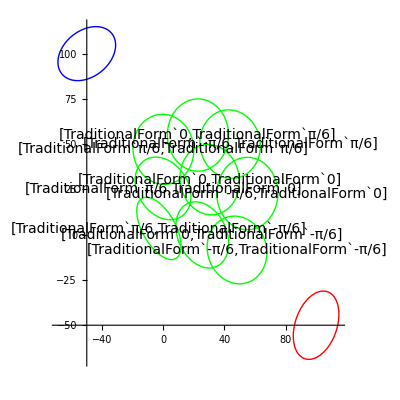

```mathematica
a=
```

```mathematica
a
```

```mathematica
scanRot = RotationMatrix[π,{1,1,1}];
pV1 =scanRot.{1,0,0}
pV2 =scanRot.{0,1,0}
```

{-1/3,2/3,2/3}

{2/3,-1/3,2/3}

```mathematica
tipAng =1/3 π;
ParametricPlot[
Evaluate[
Ceq1 = CircleEq[Cm1,lat1,long1,rotorLength,θ];
Ceq2 = CircleEq[Cm2,lat2,long2,rotorLength,θ];
{{Ceq1.pV1,Ceq1.pV2},
{Ceq2.pV1,Ceq2.pV2},
Table[Ceq3 = CircleEq3[Cm3,lat3,long3,rotorLength,θ,θxV,θyV];
{Ceq3.pV1,Ceq3.pV2},{θxV,{0,-π/6}},{θyV,{0,π/6}}]}],
{θ,0,2π},AspectRatio->Automatic, PlotStyle->{Red,Blue,Green}
]
```

-Graphics-

```mathematica
RotationMatrix[π/4,{1,-1,0}].{1,0,0}
RotationMatrix[π/4,{1,-1,0}].{0,1,0}
```

{1/4 (2+√2),1/4 (-2+√2),1/2}

{1/4 (-2+√2),1/4 (2+√2),1/2}

```mathematica
Table[RotationMatrix[π/4,{1,-1,0}].v,{v,{{1,1,0},{1,-1,0},{-1,-1,0},{-1,1,0}}}]
```

{{1/4 (-2+√2)+1/4 (2+√2),1/4 (-2+√2)+1/4 (2+√2),1},{1/4 (2-√2)+1/4 (2+√2),1/4 (-2-√2)+1/4 (-2+√2),0},{1/4 (-2-√2)+1/4 (2-√2),1/4 (-2-√2)+1/4 (2-√2),-1},{1/4 (-2-√2)+1/4 (-2+√2),1/4 (2-√2)+1/4 (2+√2),0}}

```mathematica
-
```

{1/4 (-2+√2)+1/4 (2+√2),1/4 (-2+√2)+1/4 (2+√2),1}

```mathematica
RotationMatrix[ArcTan[z,x],{0,1,0}].RotationMatrix[ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}].{-1/(√2)gearbox3Length,-1/(√2)gearbox3Length,baseHingeHeight+hoopRad};
```

```mathematica
Clear[n,u,v,RotM,C3rot,xyzNorm,x,y,z,θy,θx]
```